# Quantum Mechanics and Hydrogen Atoms

## Plots, Wavefunctions, and Probability Clouds

Physics 230: Final Presentation

Aaron Jenkins and Daniel Manning

Brigham Young University

4/18/2026

## Uncertainty

### Classical Uncertainty: Waves

Uncertainty relations had been a well-known phenomenon for decades prior to the development of quantum mechanics. To explain what an uncertainty relation actually is, we need to define what a wave packet is. A single sine wave has a well-defined wavelength, amplitude, and phase. A wave packet is the summation of many similar sine waves that results in there being a large centralized peak at the center, and then to the left and right of that peak the amplitude asymptotically approaches zero. The following example demonstrates a wave packet.

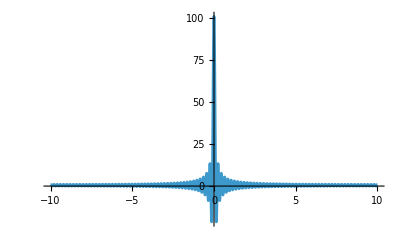

```mathematica
y1[x_]:=Sum[Cos[2Pi*(n/20)*x],{n,0,100}]
Plot[y1[x],{x,-10,10},PlotRange->All]
```

The following are other examples of a wave packets. Note the summation limits and their corresponding result on the wave packet.

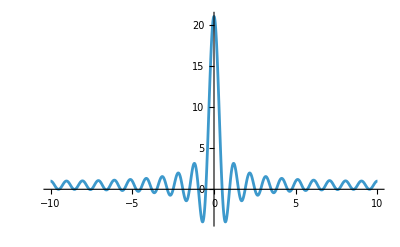

```mathematica
y2[x_]:=Sum[Cos[2Pi*(n/20)*x],{n,0,20}]
Plot[y2[x],{x,-10,10},PlotRange->All]
```

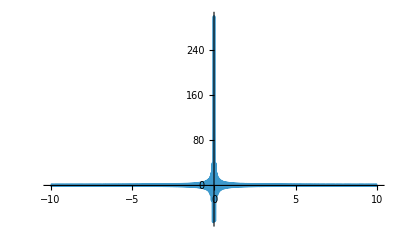

```mathematica
y3[x_]:=Sum[Cos[2Pi*(n/20)*x],{n,0,300}]
Plot[y3[x],{x,-10,10},PlotRange->All]
```

As n increments, the frequency of the wave added to the wave packet also changes. Adding up a huge range of frequencies results in a very large, centralized peak that spreads out very little. Adding up only a few frequencies results in a small peak that spreads out a lot. A high uncertainty in frequency (resulting from the large number of distinct frequencies added) results in low positional uncertainty (the wave packet has a small expanse in x). This concept is the core of uncertainty relations: basically, the more certain your frequency is, the less certain the spatial position is. This concept is absolutely essential to understanding quantum mechanics.

### Uncertainty in Matter: de Broglie waves

The key breakthrough in quantum mechanics was the model of viewing particles like waves, rather than physical objects. A PhD candidate named Louis de Broglie proposed that electrons behaved this way, as shown by the double-slit experiment with an electron beam rather than with light. Electrons passing through the slits diffract in a very similar way to light, strongly suggesting that electrons have wavelike nature in addition to their typical conceptualization as particles. Matter waves are clearly not strictly the same as something like light; instead, the square of the amplitude of a de Broglie wave (as it came to be called) represented the probability that a particle is going to be found there when measured. The de Broglie wavelength of any given particle is given by λ=h/p, where h is the physical constant and p is the momentum of the particle.

Suppose that the first wave packet above (replicated below for convenience) describes an electron. The large centralized peak indicates a very high probability that the electron will be found there, while the very low amplitude at x>5 indicates a very low probability that the electron will be found there. Since the wavelength of the waves depends on the momentum, the frequency does too. Uncertainty in frequency and position are related, as already shown above. The math leads to an uncertainty relation between Δx, the uncertainty in position, and Δp, the uncertainty in momentum. Written explicitly, Δx*Δp ≥ ℏ/2. There are many such uncertainty relations with quantum mechanics, but for our purposes in modeling electron orbitals, this is the most important one. It is physically impossible for a particle to have both a well-defined speed and a well-defined position in the same axis at the same time. This is known as the Heisenberg Uncertainty Principle.

```mathematica
Plot[y1[x],{x,-10,10},PlotRange->All]
```

-Graphics-

Because of positional uncertainty, the Bohr model assumption of fixed orbital distances cannot be correct. While the Bohr radius is incorrect, the idea of energy levels proved to be a valuable one, and in the notebook on quantum numbers, the exact use of energy levels will be explored.